# MATRIX STRUCTURE

## For the coupling matrices of the S_1 leptoquark introducing a FN symmetry

## Initialization and constants

```mathematica
hbar=6.582119*10^-25; (*GeV*s*)
secPerYear=3600*24*365.25;
hbary=hbar/secPerYear;

(* CKM and PMNS matrices *)
V= {{0.97435,0.22501,0.00373},{0.22487,0.97349,0.04183},{0.00858,0.04111,0.99912}};
U={{0.82296,0.54843,0.14815},{0.27528,0.61286,0.74069},{0.49695,0.56888,0.65531}};

(* 3rd generation charges *)
Qq3=0;
Ql3=0;
QuR3=0;
QdR3=0;
QeR3=0; 

(* masses in GeV *)
mp=0.938272;
me=0.000511;
mmu=0.105658;
mpi0=0.134977;
mpiPlus=0.139570;
mK=0.493677;
meta = 0.54786;
mrho0=0.77503;
mrhoPlus=0.77511;
momega=0.78266;
mK0=0.49761;
mLQ=10000; (*10 TeV*)
Lambda= 10^16; (*GeV*) (* GUT scale *)

(* Running coupling and Lattice QCD parameters *)
AL = 1.4;
W0benchmark= 0.1;
(* Lattice QCD form factor *)
W0EpiL= 0.134;
W0EpiR=-0.131;
W0MupiL=0.119;
W0MupiR=-0.118;
W0NupiL=0.189;
W0NupiR=-0.186;
W0NuKR=-0.134;
W0NuKL=0.139;
W0EetaR=0.006;
W0EetaL=0.113;
W0MuetaR=0.011;
W0MuetaL=0.108;


(* CM momentums: p=(1/(2mp))*Sqrt[(mp^2-mf1^2-mf2^2)^2-4*mf1^2*mf2^2] *)
pepi0=(1/(2*mp))*Sqrt[(mp^2-me^2-mpi0^2)^2-4*me^2*mpi0^2];
pmupi0=(1/(2*mp))*Sqrt[(mp^2-mmu^2-mpi0^2)^2-4*mmu^2*mpi0^2];
pnupiPlus=(1/(2*mp))*(mp^2-mpiPlus^2);
pnuK=(1/(2*mp))*(mp^2-mK^2);
peeta=(1/(2*mp))*Sqrt[(mp^2-me^2-meta^2)^2-4*me^2*meta^2];
pmueta=(1/(2*mp))*Sqrt[(mp^2-mmu^2-meta^2)^2-4*mmu^2*meta^2];
perho=(1/(2*mp))*Sqrt[(mp^2-me^2-mrho0^2)^2-4*me^2*mrho0^2];
pmurho=(1/(2*mp))*Sqrt[(mp^2-mmu^2-mrho0^2)^2-4*mmu^2*mrho0^2];
pnurho=(1/(2*mp))*(mp^2-mrhoPlus^2);
peomega=(1/(2*mp))*Sqrt[(mp^2-me^2-momega^2)^2-4*me^2*momega^2];
pmuomega=(1/(2*mp))*Sqrt[(mp^2-mmu^2-momega^2)^2-4*mmu^2*momega^2];
peK0=(1/(2*mp))*Sqrt[(mp^2-me^2-mK0^2)^2-4*me^2*mK0^2];
pmuK0=(1/(2*mp))*Sqrt[(mp^2-mmu^2-mK0^2)^2-4*mmu^2*mK0^2];

(* K prefactors assuming the leptoquark mass is inside this because we are taking it as a constant *)
KEpi0 = pepi0/(16*Pi*mp^2)*AL^2/mLQ^4*(mp^2+me^2-mpi0^2);
KMupi0= pmupi0/(16*Pi*mp^2)*AL^2/mLQ^4*(mp^2+mmu^2-mpi0^2);
KNupiPlus=pnupiPlus/(16*Pi*mp^2)*AL^2/mLQ^4*(mp^2-mpiPlus^2);
KNuK=pnuK/(16*Pi*mp^2)*AL^2/mLQ^4*(mp^2-mK^2);
KEeta=peeta/(16*Pi*mp^2)*AL^2/mLQ^4*(mp^2+me^2-meta^2);
KMueta=pmueta/(16*Pi*mp^2)*AL^2/mLQ^4*(mp^2+mmu^2-meta^2);
KErho0= perho/(16*Pi*mp^2)*(AL^2 * W0benchmark^2)/mLQ^4*(mp^2+me^2-mrho0^2);
KMurho0=pmurho/(16*Pi*mp^2)*(AL^2 * W0benchmark^2)/mLQ^4*(mp^2+mmu^2-mrho0^2);
KNurhoPlus = pnurho/(16*Pi*mp^2)*(AL^2 * W0benchmark^2)/mLQ^4*(mp^2-mrhoPlus^2);
KEomega=peomega/(16*Pi*mp^2)*(AL^2 * W0benchmark^2)/mLQ^4*(mp^2+me^2-momega^2);
KMuomega=pmuomega/(16*Pi*mp^2)*(AL^2 * W0benchmark^2)/mLQ^4*(mp^2+mmu^2-momega^2);
```

```mathematica
(* PDG experimental bounds (in years)*)
limEpi=2.4*10^34;
limMupi=1.6*10^34;
limNuPi=3.9*10^32;
limNuK=5.9*10^34;
limEeta=1.0*10^34;
limMueta=4.7*10^33;
limErho=7.2*10^32;
limMurho=5.7*10^32;
limNurho=1.62*10^32;
limEomega=1.6*10^33;
limMuomega=2.8*10^33;
```

## MC scan

### Core

```mathematica
(*This function searches in the parameter space for variables that fit the PDG limits*)ScanProtonDecay[nLimits_,numSamples_,maxCharge_]:=Module[{results={},safetyFactors,minRobustness,bottleneckIdx,channelNames,bottleneck},
channelNames={"p->e+pi0","pi->mu+pi0","pi->nupi+","p->nuK+"};
Do[(*Assign random values to the exponents*)
{Qq1,Qq2}=ReverseSort[RandomSample[Range[0,maxCharge],2]];
{QuR1,QuR2}=ReverseSort[RandomSample[Range[0,maxCharge],2]];
{QdR1,QdR2}=ReverseSort[RandomSample[Range[0,maxCharge],2]];
{Ql1,Ql2}=ReverseSort[RandomSample[Range[0,maxCharge],2]];
{QeR1,QeR2}=ReverseSort[RandomSample[Range[0,maxCharge],2]];
(*Qlq=RandomInteger[{-10,10}];*)
eps=RandomReal[{10^-1,0.5}];
(*Reconstruct the coupling matrices*)y1LL={{eps^Abs[Qq1+Ql1],eps^Abs[Qq1+Ql2],eps^Abs[Qq1+Ql3]},{eps^Abs[Qq2+Ql1],eps^Abs[Qq2+Ql2],eps^Abs[Qq2+Ql3]},{eps^Abs[Qq3+Ql1],eps^Abs[Qq3+Ql2],eps^Abs[Qq3+Ql3]}};
z1LL={{eps^Abs[2*Qq1],eps^Abs[Qq1+Qq2],eps^Abs[Qq1+Qq3]},{eps^Abs[Qq1+Qq2],eps^Abs[2*Qq2],eps^Abs[Qq2+Qq3]},{eps^Abs[Qq1+Qq3],eps^Abs[Qq2+Qq3],eps^Abs[2*Qq3]}};
y1RR={{eps^Abs[QuR1+QeR1],eps^Abs[QuR1+QeR2],eps^Abs[QuR1+QeR3]},{eps^Abs[QuR2+QeR1], eps^Abs[QuR2+QeR2],eps^Abs[QuR2+QeR3]},{eps^Abs[QuR3+QeR1],eps^Abs[QuR3+QeR2],eps^Abs[QuR3+QeR3]}};
z1RR={{eps^Abs[QuR1+QdR1], eps^Abs[QuR1+QdR2],eps^Abs[QuR1+QdR3]},{eps^Abs[QuR2+QdR1],eps^Abs[QuR2+QdR2],eps^Abs[QuR2+QdR3]},{eps^Abs[QuR3+QdR1],eps^Abs[QuR3+QdR2],eps^Abs[QuR3+QdR3]}};
(*Effective matrices*)
yEff=V.y1LL;
zEff=V.z1LL;
hEff=y1LL.U;

(*Lifetime Calculations*)
tauEpi0=hbary/(KEpi0*(Abs[(W0EpiL*zEff[[1,1]]+W0EpiR*z1RR[[1,1]])*yEff[[1,1]]]^2 + Abs[(W0EpiL*zEff[[1,1]]+W0EpiR*z1RR[[1,1]])*y1RR[[1,1]]]^2));
tauMupi=hbary/(KMupi0*(Abs[(W0MupiL*zEff[[1,1]]+W0MupiR*z1RR[[1,1]])*yEff[[1,2]]]^2 + Abs[(W0MupiL*zEff[[1,1]]+W0MupiR*z1RR[[1,1]])*y1RR[[1,2]]]^2 ));
tauNuPi=hbary/(KNupiPlus*(Abs[(W0NupiL*zEff[[1,1]]+W0NupiR*z1RR[[1,1]])*(hEff[[1,1]]+hEff[[1,2]]+hEff[[1,3]])]^2 ));
tauNuK=hbary/(KNuK*(Abs[(W0NuKL*zEff[[1,1]]+W0NuKR*z1RR[[1,1]])*(hEff[[2,1]]+hEff[[2,2]]+hEff[[2,3]])]^2 ));
(*VEV calculation*)
Vev=eps*Lambda;(*GeV*)

(*Acumulative filter for each number of limits fulfilled*)isOk=Which[nLimits==1,tauEpi0>limEpi,nLimits==2,tauEpi0>limEpi&&tauMupi>limMupi,nLimits==3,tauEpi0>limEpi&&tauMupi>limMupi&&tauNuPi>limNuPi,nLimits==4,tauEpi0>limEpi&&tauMupi>limMupi&&tauNuPi>limNuPi&&tauNuK>limNuK];
If[isOk,
safetyFactors={tauEpi0/limEpi,tauMupi/limMupi,tauNuPi/limNuPi,tauNuK/limNuK};
minRobustness=Min[safetyFactors];
bottleneckIdx=Ordering[safetyFactors,1][[1]];
bottleneck=channelNames[[bottleneckIdx]];

AppendTo[results,{eps,Qq1,Qq2,Qq3,Ql1,Ql2,Ql3,QuR1,QuR2,QuR3,QdR1,QdR2,QdR3,QeR1,QeR2,QeR3,minRobustness,bottleneck}]],{numSamples}];

cleanResults=DeleteDuplicates[results];

Return[results]];
```

### Minimum value of maxCharge

```mathematica
chargeThresholdTest=Table[{mCharge,Length[ScanProtonDecay[4,1000,mCharge]]},{mCharge,1,20}];
Grid[Prepend[chargeThresholdTest,{"Max Charge","Valid Solutions"}],Frame->All]
```

Max Charge | Valid Solutions
1 | 0
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0
9 | 0
10 | 0
11 | 0
12 | 0
13 | 0
14 | 4
15 | 0
16 | 10
17 | 16
18 | 23
19 | 34
20 | 40

### Ejecution

```mathematica
(*Ejecution for x limits and y iterations*)
mysolutions=ScanProtonDecay[4,100000,20];

Print["Number of solutions found: ",Length[mysolutions]];
sortedSolutions=SortBy[mysolutions,#[[17]]&];

If[Length[mysolutions]>0,TableForm[Take[sortedSolutions,Min[Length[sortedSolutions],10]],TableHeadings->{None,{"eps","Qq1","Qq2","Qq3","Ql1","Ql2","Ql3","QuR1","QuR2","QuR3","QdR1","QdR2","QdR3","QeR1","QeR2","QeR3","lowest robustness factor","less robust channel"}}]]
```

Number of solutions found: 4084

eps | Qq1 | Qq2 | Qq3 | Ql1 | Ql2 | Ql3 | QuR1 | QuR2 | QuR3 | QdR1 | QdR2 | QdR3 | QeR1 | QeR2 | QeR3 | lowest robustness factor | less robust channel
0.133871 | 19 | 9 | 0 | 7 | 6 | 0 | 9 | 2 | 0 | 9 | 5 | 0 | 15 | 11 | 0 | 1.00271 | p->nuK+
0.153412 | 19 | 7 | 0 | 18 | 7 | 0 | 20 | 15 | 0 | 19 | 4 | 0 | 14 | 7 | 0 | 1.00409 | p->nuK+
0.175386 | 16 | 12 | 0 | 18 | 10 | 0 | 12 | 10 | 0 | 15 | 5 | 0 | 20 | 8 | 0 | 1.00654 | p->nuK+
0.120115 | 18 | 5 | 0 | 18 | 9 | 0 | 19 | 5 | 0 | 14 | 1 | 0 | 13 | 7 | 0 | 1.00877 | p->nuK+
0.134666 | 16 | 12 | 0 | 15 | 5 | 0 | 17 | 16 | 0 | 18 | 14 | 0 | 17 | 9 | 0 | 1.01046 | pi->mu+pi0
0.268567 | 19 | 18 | 0 | 16 | 14 | 0 | 19 | 11 | 0 | 6 | 3 | 0 | 12 | 11 | 0 | 1.01238 | p->nuK+
0.130431 | 20 | 4 | 0 | 20 | 5 | 0 | 3 | 2 | 0 | 20 | 4 | 0 | 14 | 0 | 0 | 1.01704 | pi->mu+pi0
0.234106 | 19 | 15 | 0 | 13 | 10 | 0 | 18 | 4 | 0 | 16 | 5 | 0 | 15 | 11 | 0 | 1.01744 | pi->mu+pi0
0.196921 | 16 | 14 | 0 | 12 | 10 | 0 | 14 | 12 | 0 | 16 | 0 | 0 | 14 | 9 | 0 | 1.02107 | p->nuK+
0.172979 | 19 | 9 | 0 | 19 | 5 | 0 | 20 | 11 | 0 | 14 | 7 | 0 | 16 | 5 | 0 | 1.02257 | pi->mu+pi0

### Epsilon Histogram

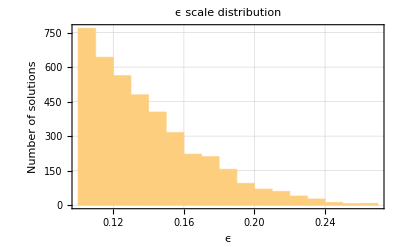

```mathematica
epsData=mysolutions[[All,1]];
tuGrafico=Histogram[epsData,20,PlotLabel->"ϵ scale distribution",Frame->True,FrameLabel->{"ϵ","Number of solutions"},GridLines->Automatic,BaseStyle->{FontSize->14,FontFamily->"Helvetica"}]
```

### Charge distribution

```mathematica
(* function defining the common style of all plots *)
myPlot[data_,title_,xLabel_,yLabel_]:=ListPlot[data,PlotStyle->{Directive[Red,Opacity[0.6],PointSize[Medium]],Directive[Blue,Opacity[0.6],PointSize[Medium]]},PlotLabel->title,Frame->True,FrameLabel->{xLabel,yLabel},GridLines->Automatic,PlotRange->{{0,20},{0,20}},AspectRatio->1,PlotLegends->{"0.1 ⩽ ϵ ⩽ 0.15","ϵ > 0.15"},BaseStyle->{FontSize->14,FontFamily->"Helvetica"}];
```

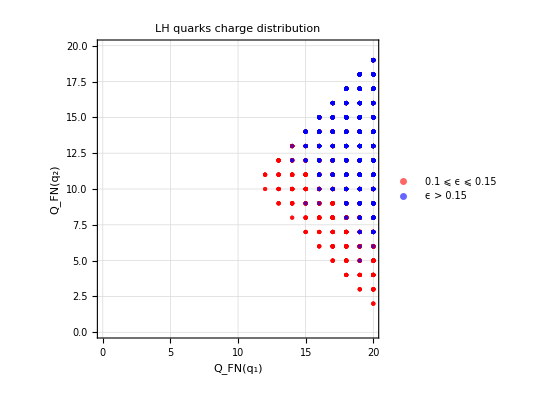

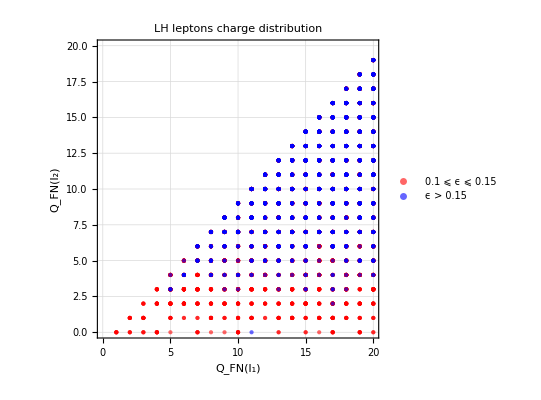

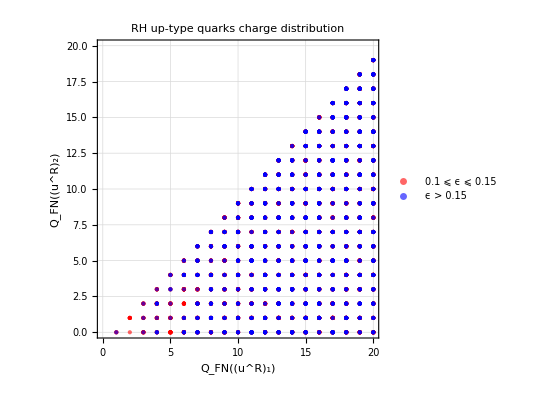

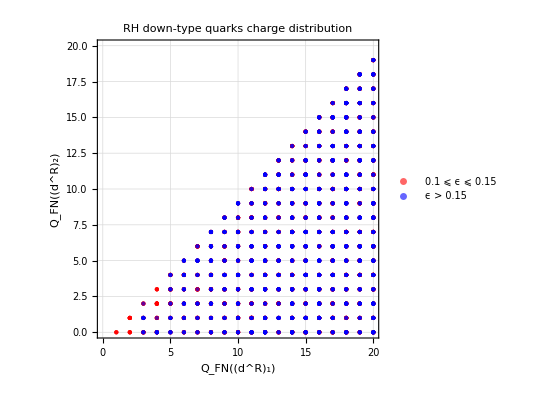

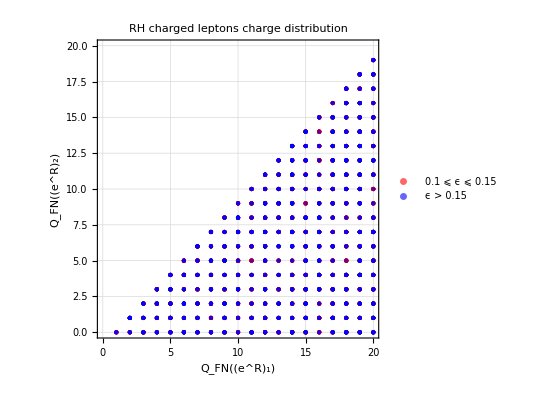

```mathematica
redSolutions=Select[mysolutions,0.1<=#[[1]]<=0.15&];
blueSolutions=Select[mysolutions,#[[1]]>0.15&];

myPlot[{redSolutions[[All,{2,3}]],blueSolutions[[All,{2,3}]]},"LH quarks charge distribution","\!\(\*SubscriptBox[\(Q\), \(FN\)]\)(\!\(\*SubscriptBox[\(q\), \(1\)]\))","\!\(\*SubscriptBox[\(Q\), \(FN\)]\)(\!\(\*SubscriptBox[\(q\), \(2\)]\))"]

myPlot[{redSolutions[[All,{5,6}]],blueSolutions[[All,{5,6}]]},"LH leptons charge distribution","\!\(\*SubscriptBox[\(Q\), \(FN\)]\)(\!\(\*SubscriptBox[\(l\), \(1\)]\))","\!\(\*SubscriptBox[\(Q\), \(FN\)]\)(\!\(\*SubscriptBox[\(l\), \(2\)]\))"]

myPlot[{redSolutions[[All,{8,9}]],blueSolutions[[All,{8,9}]]},"RH up-type quarks charge distribution","\!\(\*SubscriptBox[\(Q\), \(FN\)]\)(\!\(\*SubscriptBox[SuperscriptBox[\(u\), \(R\)], \(1\)]\))","\!\(\*SubscriptBox[\(Q\), \(FN\)]\)(\!\(\*SubscriptBox[SuperscriptBox[\(u\), \(R\)], \(2\)]\))"]

myPlot[{redSolutions[[All,{11,12}]],blueSolutions[[All,{11,12}]]},"RH down-type quarks charge distribution","\!\(\*SubscriptBox[\(Q\), \(FN\)]\)(\!\(\*SubscriptBox[SuperscriptBox[\(d\), \(R\)], \(1\)]\))","\!\(\*SubscriptBox[\(Q\), \(FN\)]\)(\!\(\*SubscriptBox[SuperscriptBox[\(d\), \(R\)], \(2\)]\))"]

myPlot[{redSolutions[[All,{14,15}]],blueSolutions[[All,{14,15}]]},"RH charged leptons charge distribution","\!\(\*SubscriptBox[\(Q\), \(FN\)]\)(\!\(\*SubscriptBox[SuperscriptBox[\(e\), \(R\)], \(1\)]\))","\!\(\*SubscriptBox[\(Q\), \(FN\)]\)(\!\(\*SubscriptBox[SuperscriptBox[\(e\), \(R\)], \(2\)]\))"]
```

## Visualization: interactive sliders

```mathematica
(*--- MANIPULATE ---*)
Manipulate[
(*Matrices Definition*)
y1LL={{eps^Abs[Qq1+Ql1],eps^Abs[Qq1+Ql2],eps^Abs[Qq1+Ql3]},{eps^Abs[Qq2+Ql1],eps^Abs[Qq2+Ql2],eps^Abs[Qq2+Ql3]},{eps^Abs[Qq3+Ql1],eps^Abs[Qq3+Ql2],eps^Abs[Qq3+Ql3]}};
z1LL={{eps^Abs[2*Qq1],eps^Abs[Qq1+Qq2],eps^Abs[Qq1+Qq3]},{eps^Abs[Qq1+Qq2],eps^Abs[2*Qq2],eps^Abs[Qq2+Qq3]},{eps^Abs[Qq1+Qq3],eps^Abs[Qq2+Qq3],eps^Abs[2*Qq3]}};
y1RR={{eps^Abs[QuR1+QeR1],eps^Abs[QuR1+QeR2],eps^Abs[QuR1+QeR3]},{eps^Abs[QuR2+QeR1], eps^Abs[QuR2+QeR2],eps^Abs[QuR2+QeR3]},{eps^Abs[QuR3+QeR1],eps^Abs[QuR3+QeR2],eps^Abs[QuR3+QeR3]}};
z1RR={{eps^Abs[QuR1+QdR1], eps^Abs[QuR1+QdR2],eps^Abs[QuR1+QdR3]},{eps^Abs[QuR2+QdR1],eps^Abs[QuR2+QdR2],eps^Abs[QuR2+QdR3]},{eps^Abs[QuR3+QdR1],eps^Abs[QuR3+QdR2],eps^Abs[QuR3+QdR3]}};

(*Effective Matrices*)
yEff=V.y1LL;
zEff=V.z1LL;
hEff=y1LL.U;

(*Lifetime Calculations*)
tauEpi0=hbary/(KEpi0*(Abs[(W0EpiL*zEff[[1,1]]+W0EpiR*z1RR[[1,1]])*yEff[[1,1]]]^2 + Abs[(W0EpiL*zEff[[1,1]]+W0EpiR*z1RR[[1,1]])*y1RR[[1,1]]]^2));
tauMupi=hbary/(KMupi0*(Abs[(W0MupiL*zEff[[1,1]]+W0MupiR*z1RR[[1,1]])*yEff[[1,2]]]^2 + Abs[(W0MupiL*zEff[[1,1]]+W0MupiR*z1RR[[1,1]])*y1RR[[1,2]]]^2 ));
tauNuPi=hbary/(KNupiPlus*(Abs[(W0NupiL*zEff[[1,1]]+W0NupiR*z1RR[[1,1]])*(hEff[[1,1]]+hEff[[1,2]]+hEff[[1,3]])]^2 ));
tauNuK=hbary/(KNuK*(Abs[(W0NuKL*zEff[[1,1]]+W0NuKR*z1RR[[1,1]])*(hEff[[2,1]]+hEff[[2,2]]+hEff[[2,3]])]^2 ));

tauEeta=hbary/(KEeta*(Abs[(zEff[[1,1]]+z1RR[[1,1]])*yEff[[1,1]]]^2+Abs[(zEff[[1,1]]+z1RR[[1,1]])*y1RR[[1,1]]]^2));
tauMueta=hbary/(KMueta*(Abs[zEff[[1,1]]*yEff[[1,2]]]^2 + Abs[zEff[[1,1]]*y1RR[[1,2]]]^2 + Abs[z1RR[[1,1]]*yEff[[1,2]]]^2 + Abs[z1RR[[1,1]]*y1RR[[1,2]]]^2));
tauErho=tauEpi0*KEpi0/KErho0;
tauMurho=tauMueta*KMueta/KMurho0;
tauNurhoPlus=hbary/(KNurhoPlus*(Abs[zEff[[1,1]]*(hEff[[1,1]]+hEff[[1,2]]+hEff[[1,3]])]^2 + Abs[z1RR[[1,1]]*(hEff[[1,1]]+hEff[[1,2]]+hEff[[1,3]])]^2));
tauEomega=tauEeta*KEeta/KEomega;
tauMuomega=tauMueta*KMueta/KMuomega;

(*Visualization*)Column[{Style["Coupling Matrices (Flavor Basis)",Bold,16],Row[{Style["y1LL = ",14],MatrixForm[y1LL],Spacer[30],Style["z1LL = ",14],MatrixForm[z1LL]}],Spacer[15],(*Nueva fila para separar las matrices RH de las LH*)Row[{Style["y1RR = ",14],MatrixForm[y1RR],Spacer[30],Style["z1RR = ",14],MatrixForm[z1RR]}],Spacer[20],Grid[{{Style["Results: Proton lifetime (years)",Bold,16]},{Grid[{{Style["Channel",Bold],Style["Theoretical Tau [years]",Bold],Style["PDG bound [years]",Bold],Style["Status",Bold]},{"p → \!\(\*SuperscriptBox[\(e\), \(+\)]\) \!\(\*SuperscriptBox[\(π\), \(0\)]\)",ScientificForm[tauEpi0,3],ScientificForm[limEpi,3],If[tauEpi0>limEpi,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},{"p → \!\(\*SuperscriptBox[\(μ\), \(+\)]\) \!\(\*SuperscriptBox[\(π\), \(0\)]\)",ScientificForm[tauMupi,3],ScientificForm[limMupi,3],If[tauMupi>limMupi,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},{"p → \!\(\*OverscriptBox[\(ν\), \(_\)]\) \!\(\*SuperscriptBox[\(π\), \(+\)]\)",ScientificForm[tauNuPi,3],ScientificForm[limNuPi,3],If[tauNuPi>limNuPi,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},{"p → \!\(\*OverscriptBox[\(ν\), \(_\)]\) \!\(\*SuperscriptBox[\(K\), \(+\)]\)",ScientificForm[tauNuK,3],ScientificForm[limNuK,3],If[tauNuK>limNuK,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},{"p → \!\(\*SuperscriptBox[\(e\), \(+\)]\) η",ScientificForm[tauEeta,3],ScientificForm[limEeta,3],If[tauEeta>limEeta,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},{"p → \!\(\*SuperscriptBox[\(μ\), \(+\)]\) η",ScientificForm[tauMueta,3],ScientificForm[limMueta,3],If[tauMueta>limMueta,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},{"p → \!\(\*SuperscriptBox[\(e\), \(+\)]\) \!\(\*SuperscriptBox[\(ρ\), \(0\)]\)",ScientificForm[tauErho,3],ScientificForm[limErho,3],If[tauErho>limErho,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},{"p → \!\(\*SuperscriptBox[\(μ\), \(+\)]\) \!\(\*SuperscriptBox[\(ρ\), \(0\)]\)",ScientificForm[tauMurho,3],ScientificForm[limMurho,3],If[tauMurho>limMurho,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},{"p → \!\(\*OverscriptBox[\(ν\), \(_\)]\) \!\(\*SuperscriptBox[\(ρ\), \(+\)]\)",ScientificForm[tauNurhoPlus,3],ScientificForm[limNurho,3],If[tauNurhoPlus>limNurho,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},{"p → \!\(\*SuperscriptBox[\(e\), \(+\)]\) ω",ScientificForm[tauEomega,3],ScientificForm[limEomega,3],If[tauEomega>limEomega,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},{"p → \!\(\*SuperscriptBox[\(μ\), \(+\)]\) ω",ScientificForm[tauMuomega,3],ScientificForm[limMuomega,3],
If[tauMuomega>limMuomega,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]}},Frame->All,Background->{None,{LightGray,White}},Alignment->Left]}}]}],
(*Explicit Controls*)
Delimiter,
Style["Global Parameters",Bold],{{eps,0.14,"ϵ"},0.01,1,Appearance->"Labeled"},
Style["Exponents y1LL & z1LL",Bold],
{{Qq1,20,"Qq1"},-20,20,1,Appearance->"Labeled"},
{{Qq2,12,"Qq2"},-20,20,1,Appearance->"Labeled"},
{{Qq3,0,"Qq3"},-20,20,1,Appearance->"Labeled"},
{{Ql1,18,"Ql1"},-20,20,1,Appearance->"Labeled"},
{{Ql2,3,"Ql2"},-20,20,1,Appearance->"Labeled"},
{{Ql3,0,"Ql3"},-20,20,1,Appearance->"Labeled"},
Delimiter,Style["Exponents RH (Quarks)",Bold],
{{QuR1,13,"QuR1"},-20,20,1,Appearance->"Labeled"},
{{QuR2,3,"QuR2"},-20,20,1,Appearance->"Labeled"},
{{QuR3,0,"QuR3"},-20,20,1,Appearance->"Labeled"},
{{QdR1,9,"QdR1"},-20,20,1,Appearance->"Labeled"},
{{QdR2,8,"QdR2"},-20,20,1,Appearance->"Labeled"},
{{QdR3,0,"QdR3"},-20,20,1,Appearance->"Labeled"},
Delimiter,Style["Exponents RH (Leptons)",Bold],
{{QeR1,9,"QeR1"},-20,20,1,Appearance->"Labeled"},
{{QeR2,3,"QeR2"},-20,20,1,Appearance->"Labeled"},
{{QeR3,0,"QeR3"},-20,20,1,Appearance->"Labeled"},ControlPlacement->Left,TrackedSymbols:>All]
```